```mathematica
Needs["WSMLink`"]
```

```mathematica
fieldL=WSMSimulate["EFieldRunner",WSMParameterValues->{{"tparticle1.x0",0},{"tparticle1.y0",0}}]
```

WSMSimulate::msg: "Error in initialization: Division by zero error. Storing results and exiting."

WSMSimulate::msg: "[error]: Division by zero. (cparticle1.dx)/(cparticle1.l ^ 3.0) evaluates to 0/0"

WSMSimulate::msg: "[error]: Division by zero. (cparticle1.dy)/(cparticle1.l ^ 3.0) evaluates to 0/0"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Split::normal: Nonatomic expression expected at position 1 in Split[Symbol, First[#2] - Last[#1] === 1 &].

First::normal: Nonatomic expression expected at position 1 in First[Symbol].

Last::normal: Nonatomic expression expected at position 1 in Last[Symbol].

First::normal: Nonatomic expression expected at position 1 in First[True].

Last::normal: Nonatomic expression expected at position 1 in Last[True].

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

WSMSimulationData[…]

```mathematica
fieldL=WSMSimulate["EFieldRunner"]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 32.865"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulationData[…]

```mathematica
fieldL["tparticle1.x"]
```

InterpolatingFunction[{{0., 32.865}}, <>]

```mathematica
xField=fieldL["tparticle1.x"]
```

InterpolatingFunction[{{0., 32.865}}, <>]

```mathematica
yField=fieldL["tparticle1.y"]
```

InterpolatingFunction[{{0., 32.865}}, <>]

```mathematica
ParametricPlot[{xField,yField},{t,0,32.86}]
```

-Graphics-

```mathematica
Show[%7,ImageSize->Large]
```

-Graphics-

```mathematica
Rasterize[%8,"Image"]
```

-Graphics-

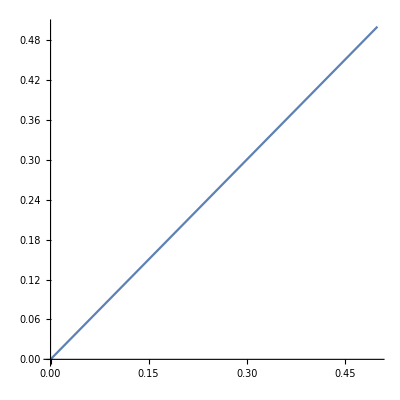

```mathematica
ParametricPlot[{0.5*u,0.5*u},{u,0,1}]
```

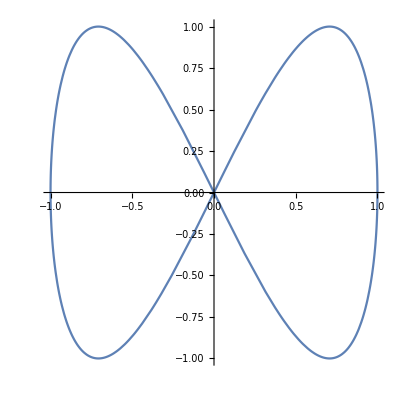

```mathematica
ParametricPlot[{Sin[u],Sin[2u]},{u,0,2Pi}]
```

```mathematica
Plot[xField,{x,0,1}]
```

-Graphics-

```mathematica
xField
```

InterpolatingFunction[{{0., 32.865}}, <>]

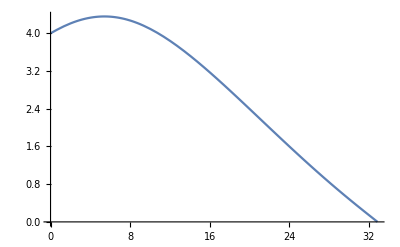

```mathematica
Plot[%20[x],{x,0.,32.86502620577364}]
```

```mathematica
yField
```

InterpolatingFunction[{{0., 32.865}}, <>]

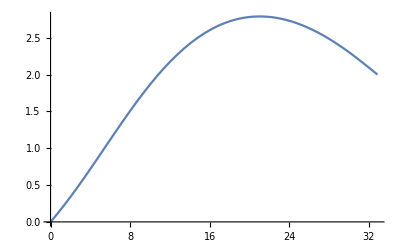

```mathematica
Plot[%22[x],{x,0.,32.86502620577364}]
```

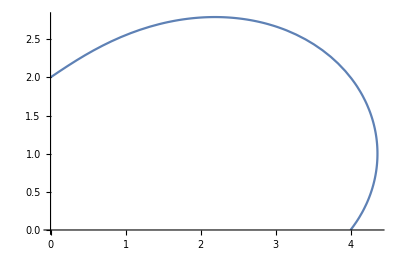

```mathematica
ParametricPlot[{%20[x],%22[x]},{x,0,32.865}]
```

```mathematica
ParametricPlot[{xField[x],yField[x]},{x,0,32.865}]
```

-Graphics-